```mathematica
(*For posterities sake, I will include problems 1 and 3 in this document, if only to have a proper formulation of problems 1 and 3 on hand*)
```

```mathematica
ρ=l/R
r=R Sin[ρ]
```

l/R

R Sin[l/R]

```mathematica
(*We can consider the area of an infinitesimal slice of S^2, a near circle
of width dl and diameter r*)
(*The total area of such a surface element would be 2 Pi a times the witdth dl*)
```

```mathematica
dl=R dρ
dA=2 Pi r dl
```

dρ R

2 dρ π R^2 Sin[l/R]

```mathematica
(*Now we can integrate this over rho and get...*)
```

```mathematica
ClearAll[ρ]
```

```mathematica
Integrate[2 Pi R^2 Sin[ρ],{ρ,0,Pi}]
```

4 π R^2

```mathematica
(*The expected result for the Surface area of a sphere*)
```

```mathematica
(*Now we can use a similar argument for showing the surface volume of S^3*)
```

```mathematica
(*We start with the formula for the volume of a shell*)
dV=4 Pi r^2
```

```mathematica
4 π r^2 dl
```

```mathematica
(*Note that r is a variable representing the radius of the sphere we integrate as we change over dl*)
```

```mathematica
r=R Sin[ρ]
dl=R dρ
```

R Sin[ρ]

dρ R

```mathematica
4 π r^2 dl
```

4 dρ π R^3 Sin[ρ]^2

```mathematica
Integrate[4 Pi R^3 (Sin[ρ])^2,ρ]
```

4 π R^3 (ρ/2-1/4 Sin[2 ρ])

```mathematica
(*Which if integrated over 0 -> Pi gives the expected*)
```

```mathematica
Integrate[4 Pi R^3 (Sin[ρ])^2,{ρ,0,Pi}]
```

2 π^2 R^3

### Question 7

```mathematica
V[ρ]= Simplify[4 π R^3 (ρ/2-1/4 Sin[2 ρ])]
```

2 π R^3 (ρ-Cos[ρ] Sin[ρ])

```mathematica
D[V[ρ],ρ]
```

2 π R^3 (1-Cos[ρ]^2+Sin[ρ]^2)

```mathematica
A[ρ]=%
```

2 π R^3 (1-Cos[ρ]^2+Sin[ρ]^2)

### Question 8

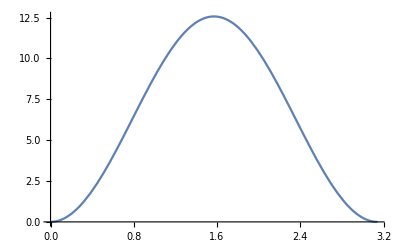

```mathematica
With[{R=1}, Plot[2 π R^3 (1-Cos[ρ]^2+Sin[ρ]^2),{ρ,0,Pi}]]
```

### Question 9

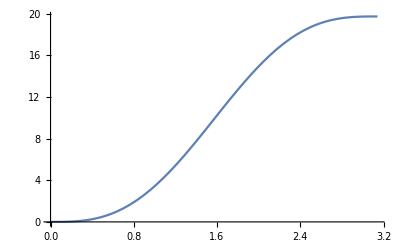

```mathematica
With[{R=1},Plot[2 π R^3 (ρ-Cos[ρ] Sin[ρ]),{ρ,0,Pi}]]
```

### Question 10

```mathematica
(*In order to find the average value of rho and rho squared we can normalize the volume function over the interval 0 to pi and then multiply rho and rho squared by that function and integrate the product*)
```

```mathematica
(*We will start by attempting to get the probability density for V[rho]*)
```

```mathematica
A=Simplify[2 π R^3 (1-Cos[ρ]^2+Sin[ρ]^2)]
```

4 π R^3 Sin[ρ]^2

```mathematica
Q=Integrate[A,{ρ,0,Pi}]
```

2 π^2 R^3

```mathematica
(*Then P[rho] is just 1/Q times A[rho]*)
```

```mathematica
P=1/Q A
```

(2 Sin[ρ]^2)/π

```mathematica
P=FullSimplify[%]
```

(2 Sin[ρ]^2)/π

```mathematica
(*Now we can take this and multiply it by rho and rho squared respectively and then integrate to find the expected value for rho and rho squared in the S^3 universe*)
```

```mathematica
P ρ
```

(2 ρ Sin[ρ]^2)/π

```mathematica
Integrate[%,{ρ,0,Pi}]
```

π/2

```mathematica
P ρ^2
```

(2 ρ^2 Sin[ρ]^2)/π

```mathematica
Integrate[%,{ρ,0,Pi}]
```

1/6 (-3+2 π^2)

### Question 11

```mathematica
ρ=n/(4/3 Pi R^3)
A=4 Pi r^2
```

(3 n)/(4 π R^3)

4 π r^2

```mathematica
ρ A
```

(3 n r^2)/R^3

```mathematica
(*We know the total density of the galaxies in the sphere as well as the area of each shell slice of the volume*)
```

```mathematica
(*Since the shell slices have differentiably small width we can use them as our measure to get the number of shperes per shell*)
```

```mathematica
ρ A Pi d^2/(4 Pi r^2)
```

(3 d^2 n)/(4 R^3)

```mathematica
Integrate[%,{r,0,R}]
```

(3 d^2 n)/(4 R)

### Question 12

```mathematica
(*We want to know at what radius (call it Subscript[r, eff]) we can place all the galaxies to get the same % of light blocked*)
```

```mathematica
(*This means we have N spheres of radius d on a shell of radiur Subscript[r, eff]*)
```

```mathematica
(*The total percentage of the area then would be the area of the projected disc divided by the total area of the shell of radius Subscript[r, eff]*)
```

```mathematica
(*Then we can equate this to the result above and find Subscript[r, eff] in terms of R*)
```

```mathematica
Solve[(3 d^2 n)/(4 R^2)==(n Pi d^2)/(4 Pi Subscript[r, eff]^2),Subscript[r, eff]]
```

{{r_eff→-R/(√3)},{r_eff→R/(√3)}}

```mathematica
Subscript[r, eff]=R/(√3)
```

R/(√3)

### Question 13

```mathematica
(*We can now attempt to do the same analysis but in the case of S^3*)
```

```mathematica
(*We start with the volume of S^3*)
```

```mathematica
ClearAll[V,A,ρ,r,R,n]
```

```mathematica
V=2 π R^3 (ρ-Cos[ρ] Sin[ρ])
A=D[V,ρ]
```

2 π R^3 (ρ-Cos[ρ] Sin[ρ])

2 π R^3 (1-Cos[ρ]^2+Sin[ρ]^2)

```mathematica
A=FullSimplify[2 π R^3 (1-Cos[ρ]^2+Sin[ρ]^2)]
```

4 π R^3 Sin[ρ]^2

```mathematica
(*Normalize the volume*)
```

```mathematica
Q=Integrate[A,{ρ,0,Pi}]
```

2 π^2 R^3

```mathematica
P=1/Q A
```

(2 Sin[ρ]^2)/π

```mathematica
(*Normalization check*)
```

```mathematica
Integrate[2 Sin[ρ]^2/Pi,{ρ,0,Pi}]
```

1

```mathematica
(*Then we can take P times the percentage light obscured in a given "shell"*)
```

```mathematica
(*Each shell has an area defined by the given value of rho*)
```

```mathematica
μ=Pi d^2/(4 Pi R^3 Sin[ρ]^2)
```

(d^2 Csc[ρ]^2)/(4 R^3)

```mathematica
P n μ
```

(d^2 n)/(2 π R^3)

```mathematica
Integrate[%,{ρ,0,Pi}]
```

(d^2 n)/(2 R^3)

```mathematica
(*Then we can find the effective distance (rho_eff) by setting it equal to the percentage of light that would be blocked if they were all set at one value of rho*)
```

```mathematica
Solve[d^2 n/(2 R^3)==(n Pi d^2)/(4 Pi R^3 Sin[Subscript[ρ, eff]]^2),Subscript[ρ, eff]]
```

{{ρ_eff→ConditionalExpression[-π/4+2 π C[1], C[1]∈ℤ]},{ρ_eff→ConditionalExpression[π/4+2 π C[1], C[1]∈ℤ]},{ρ_eff→ConditionalExpression[(3 π)/4+2 π C[1], C[1]∈ℤ]},{ρ_eff→ConditionalExpression[(5 π)/4+2 π C[1], C[1]∈ℤ]}}

```mathematica
Subscript[ρ, eff]=ConditionalExpression[π/4+2 π C[1],C[1]∈Integers]
```

ConditionalExpression[π/4+2 π C[1], C[1]∈ℤ]

```mathematica
(*Here we can just take Subscript[c, 1] to be 0 for simplicities sake and also because this is after only a single "half turn"*)
```

```mathematica
(*Thus Subscript[rho, eff] is Pi/4*)
```